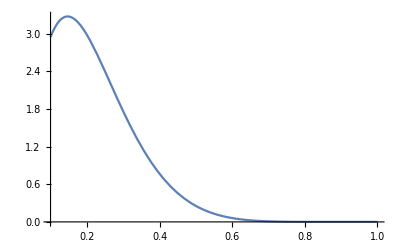

```mathematica
Plot[-I*Hdgf1u[x,-1],{x,0.1,1}]
```

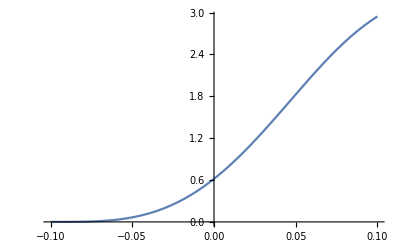

```mathematica
Plot[-I*Herf1u[x,-1],{x,-0.1,0.1}]
```

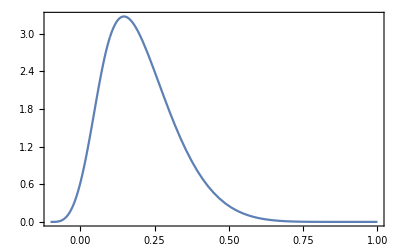
-Graphics-H_ux

```mathematica
Labeled[Show[Plot[-I*Hdgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herf1u[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","x"},{Left,Bottom}]
```

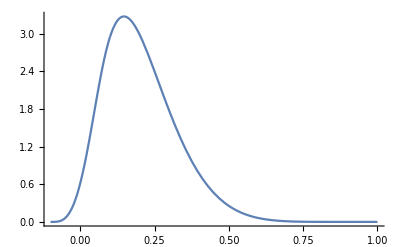

```mathematica
Show[Plot[-I*Hdgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herf1u[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

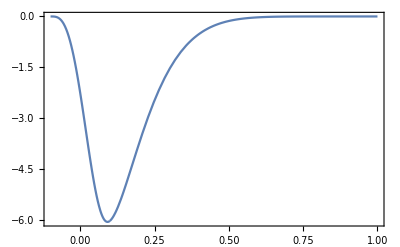
-Graphics-E_ux

```mathematica
Labeled[Show[Plot[-I*Edgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerf1u[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],{"E_u","x"},{Left,Bottom}]
```

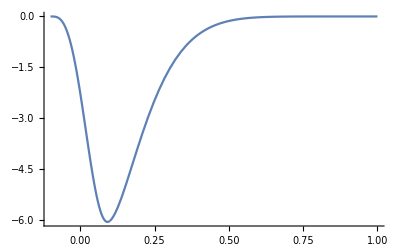

```mathematica
Show[Plot[-I*Edgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerf1u[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re\\Dterm-b-up-xi1.wdx"
```

```mathematica
Dterm=Import["G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re\\Dterm-b-up-xi1.wdx"];
HerD=Query[1,1]@Dterm;
HdaD=Query[1,2]@Dterm;

EerD=Query[2,1]@Dterm;
EdaD=Query[2,2]@Dterm;
HerDf=Interpolation[HerD];
HdaDf=Interpolation[HdaD];

EerDf=Interpolation[EerD];
EdaDf=Interpolation[EdaD];
```

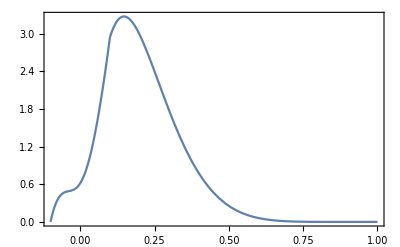
-Graphics-H_ux

```mathematica
Labeled[Show[Plot[-I*Hdgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*(Herf1u[x,-1]+HerDf[x]+HdaDf[x]),{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","x"},{Left,Bottom}]
```

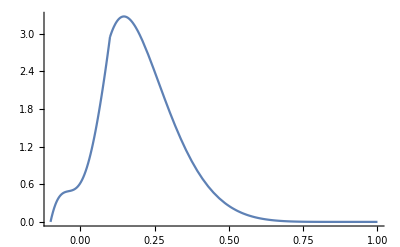

```mathematica
Show[Plot[-I*Hdgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*(Herf1u[x,-1]+HerDf[x]+HdaDf[x]),{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Herf1u[-0.1,-1]+HerDf[-0.1]+HdaDf[-0.1]
```

0.+0. ⅈ

```mathematica
Herf1u[x,-1]+HerDf[x,-1]+HdaDf[x,-1]
```

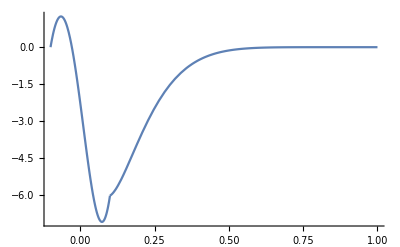

```mathematica
Show[Plot[-I*Edgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*(Eerf1u[x,-1]-EerDf[x]-EdaDf[x]),{x,-0.1,0.1},PlotRange->All]]
```

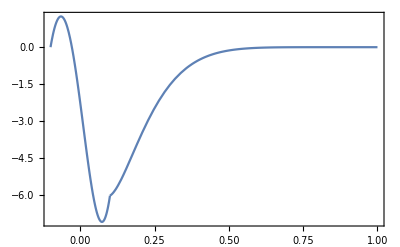
-Graphics-E_ux

```mathematica
Labeled[Show[Plot[-I*Edgf1u[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*(Eerf1u[x,-1]-EerDf[x]-EdaDf[x]),{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],{"E_u","x"},{Left,Bottom}]
```

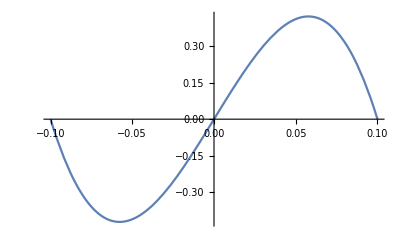

```mathematica
Plot[I*HerDf[x],{x,-0.1,0.1}]
```

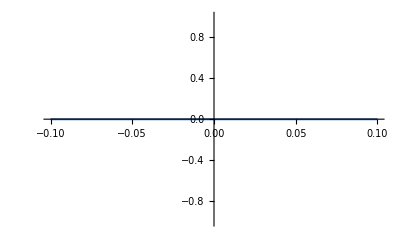

```mathematica
Plot[I*(HerDfu[x,-1]-HerDf[x]),{x,-0.1,0.1}]
```